# Arm state visualization

## Import

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__19_07_28"; (* range: 40 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__09_34_18";(* range: 50 deg *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__13_32_26";(* range: 60 deg 2*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_17__12_20_59";(* range: 60 deg *)

 dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__00_17_05";(* range: 50 deg, 2 dist *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__00_34_50";(* range: 50 deg, 2 dist *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_18__17_06_21";(* range: 50 deg, 1 dist again*)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_16__15_57_23";(* range: 50 deg *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_25__15_59_49"; (*  *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_25__16_00_05"; (* 0.781 *)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__10_54_39";(* Long line: Inc. 0.82 *)
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__12_51_07";(* Long line: 0.8823 *)
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_09_26__12_51_33";(* Long line: 0.882 *)*)

dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/Arm/13_10_07__10_29_33";(* Long line: 0.8823 *)


figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";

SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]]
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
avgfitness=Cases[fitXml,XMLElement["Generation",{_,_,"AverageFitness"->fit_},___]->fit,Infinity];
fitness=ToExpression[fitness];
avgfitness=ToExpression[avgfitness];
font="Arial";
```

{NeuralExtInput0,NeuralExtInput1,NeuralExtInput2,NeuralExtInput3,NeuralExtInput4,NeuralExtInput5,NeuralExtInput6,NeuralExtInput7,NeuralExtInput8,NeuralOutput0,NeuralOutput1,NeuralOutput2,NeuralOutput3,NeuralOutput4,NeuralOutput5,NeuralOutput6,NeuralOutput7,NeuralOutput8,NeuralState0,NeuralState1,NeuralState2,NeuralState3,NeuralState4,NeuralState5,NeuralState6,NeuralState7,NeuralState8,accelerationElbow,accelerationShoulder,angleElbow,angleShoulder,coriolisElbow,coriolisShoulder,dampingElbow,dampingShoulder,elbX,elbY,gravityElbow,gravityShoulder,inertiaElbow,inertiaShoulder,interactionElbow,interactionShoulder,lineX1,lineX2,lineY1,lineY2,torqueElbow,torqueShoulder,velocityElbow,velocityShoulder,x,y}

11000

## Fitness

{5000}

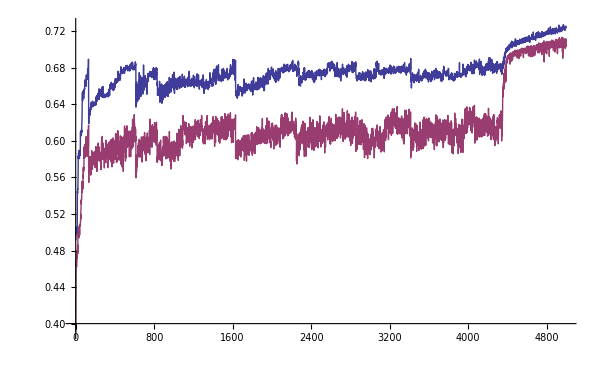

0.727158

```mathematica
Dimensions[fitness]

fit={fitness,avgfitness};
fitP =ListLinePlot[fit,PlotRange->All,ImageSize->600]
maxFit = Max[fitness]
```

## Config

```mathematica
plotOptions = {PlotJoined->True, PlotRange->All};

dt =1/200;
T=11.0;
skip=0.0;
numTrials = Round[numData/(T/dt)]

SetTrial[trial_]:=Module[{},
t0=1+(trial*T+skip)/dt;
tn= t0+((T-skip)/dt);
time=Range[tn-t0]*dt;
];

NtoI[name_]:=Position[varNames, name][[1,1]];

NtoD[name_]:=Table[data[[i,NtoI[name]]],{i,t0,tn}];

TimePlot[name_, options_, Scale_:1] := Module[{},
ListLinePlot[Transpose[{time,Scale*NtoD[name]}], Join[options,plotOptions]]
];

(*Inflate[x_,f_]:=If[x<0,(1+f)*)

XYPlot[tr_,name1_,name2_, options_] :=Module[{},
SetTrial[tr];
ListLinePlot[Transpose[{NtoD[name1],NtoD[name2]}], Join[options,plotOptions]]
];

MinExpand[x_,f_]:=If[x>=0,(1-f)*x,(1+f)*x];
MaxExpand[x_,f_]:=If[x>=0,(1+f)*x,(1-f)*x];

VarRange[v1_,v2_,f_,t0_:1,tn_:-1]:=Module[{d1,d2},
d1=data[[t0;;tn,NtoI[v1]]];
d2=data[[t0;;tn,NtoI[v2]]];
range={{MinExpand[Min[d1],f],MaxExpand[Max[d1],f]},{MinExpand[Min[d2],f],MaxExpand[Max[d2],f]}}
 ];

PlotEnvLine[t_,options_]:=Module[{x1i,x2i,y1i,y2i,x1,x2,y1,y2},
SetTrial[t];
x1i=NtoI["lineX1"];
x2i=NtoI["lineX2"];
y1i=NtoI["lineY1"];
y2i=NtoI["lineY2"];
x1 = data[[t0,x1i]];
x2 = data[[t0,x2i]];
y1 = data[[t0,y1i]];
y2 = data[[t0,y2i]];
ListLinePlot[{{x1,y1},{x2,y2}}, Join[options,plotOptions]]
];


SetTrial[0];
```

5

## Figures

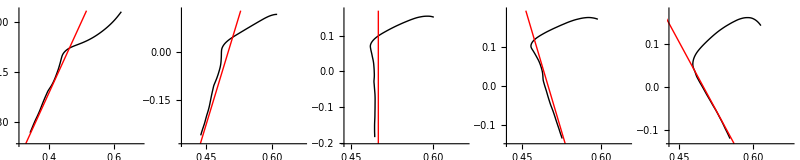

```mathematica
skip = 7;
range ={{0.2,0.7},{-0.2,0.6}};
origin={range[[1,1]],range[[2,1]]};
PlotLineTraj[t_,options_:{}]:=Module[{p1,p2,r,o},
SetTrial[t];
r=VarRange["x","y",0.1,IntegerPart[t0],IntegerPart[tn]];
o={r[[1,1]],r[[2,1]]};
p1=XYPlot[t,"x","y",Join[options,{PlotRange->r,PlotStyle->{Black},AxesOrigin->o}]];
p2= PlotEnvLine[t,Join[options,{PlotRange->r,PlotStyle->{Red}}]];
Show[p1,p2]
];

GraphicsRow[Table[PlotLineTraj[i,{AspectRatio->1}],{i,0,4}],ImageSize->800]
(*GraphicsGrid[Table[PlotLineTraj[i*(numTrials/2)+j,{AspectRatio->1}],{i,0,1},{j,0,-1+numTrials/2}],ImageSize->800]*)
```

Joint angle phase space

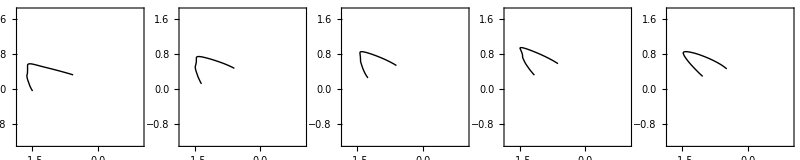

Sensor-shoulder phase space

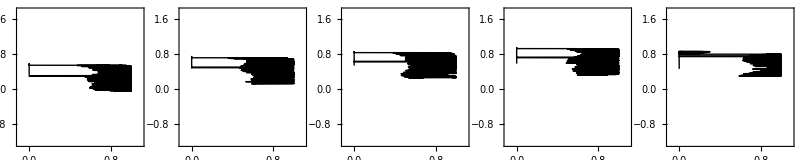

Sensor-elbow phase space

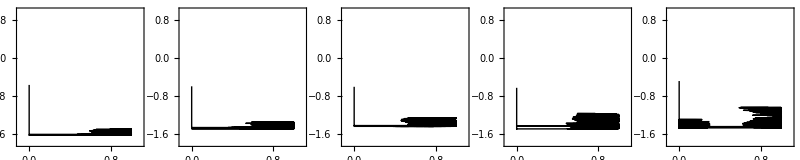

```mathematica
skip = 7;
range = {{-1.8,1},{-1.25,1.8}};
origin={range[[1,1]],range[[2,1]]};
Print["Joint angle phase space"]
GraphicsRow[Table[XYPlot[i,"angleElbow","angleShoulder",{AspectRatio->1,PlotRange->range,AxesOrigin->origin,Frame->True,PlotStyle->Black}],{i,0,4}],ImageSize->800]

range = {{-0.1,1.1},{-1.25,1.8}};
origin={range[[1,1]],range[[2,1]]};
Print["Sensor-shoulder phase space"]
GraphicsRow[Table[XYPlot[i,"NeuralExtInput0","angleShoulder",{AspectRatio->1,PlotStyle->Black,Frame->True,PlotRange->range,AxesOrigin->origin}],{i,0,4}],ImageSize->800]

range = {{-0.1,1.1},{-1.8,1}};
origin={range[[1,1]],range[[2,1]]};
Print["Sensor-elbow phase space"]
GraphicsRow[Table[XYPlot[i,"NeuralState0","angleElbow",{AspectRatio->1,PlotRange->range,PlotStyle->Black,Frame->True,AxesOrigin->origin}],{i,0,4}],ImageSize->800]
```

```mathematica
Length[time]
SetTrial[1]
Length[NtoD["NeuralOutput0"]]
```

799

800